```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Import data thief of WD mass-density + WD mass-radius relations

```mathematica
WD=Import["/Users/NewUser/Documents/Qballs/WD.csv"];
WDrad=Import["/Users/NewUser/Documents/Qballs/WDradius.csv"];
WDreverse=Reverse/@WD;
Massreverse=Interpolation[WDreverse];
WDplot=Interpolation[WD];Radplot=Interpolation[WDrad];
```

```mathematica
Convert[Radplot[1.25]SolarRadius,Kilo Meter]
```

3328.47 Kilo Meter

```mathematica
Convert[Radplot[0.85]SolarRadius,Kilo Meter]
```

6392.93 Kilo Meter

#### V_esc

```mathematica
Clear[vesc]
vesc[M_]:=Convert[Sqrt[2GravitationalConstant*M/Radplot[M]*SolarMass/SolarRadius] 1/SpeedOfLight,d]
```

```mathematica
vesc[1.25]
```

0.0333087

```mathematica
vesc[0.85]
```

0.0198191

#### λ_T as function of mass

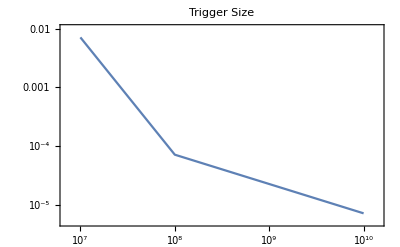

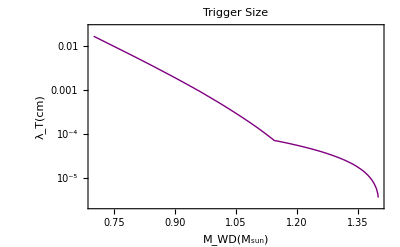

```mathematica
trigger[ρ_]:=If[ρ>10^8,10^-5*(ρ/(5*10^9))^(-1/2),1/(10000 √2)*(ρ/10^8)^-2]
triggermass=Interpolation[Table[{WDplot[logρ],trigger[10^logρ]},{logρ,5,10.5,0.01}]];
LogLogPlot[{trigger[ρ]},{ρ,10^10,10^7},PlotLabel->"Trigger Size",Frame->True]
LogPlot[triggermass[M],{M,0.7,1.4},PlotLabel->"Trigger Size",Frame->True,PlotStyle->{Thick,Purple},FrameLabel->{"M_WD(M_sun)","λ_T(cm)"},FrameStyle->Black]
```

#### E_boom (in GeV) as function of WD mass

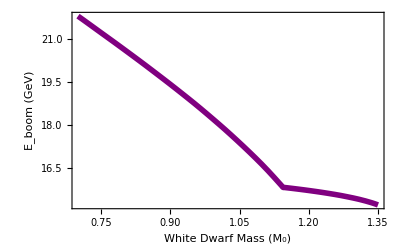

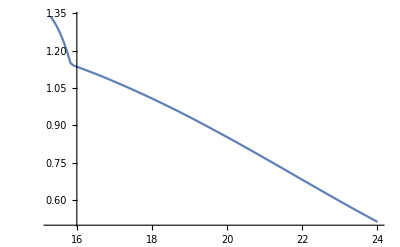

```mathematica
eboom[M_]:=Log10[Convert[(10^Massreverse[M]*Gram/Centimeter^3 SpeedOfLight^2)/(12 Giga ElectronVolt)*4 Pi/3(triggermass[M]Centimeter)^3*(Mega ElectronVolt)1/(Giga ElectronVolt),d]]
eboomreverse[mdm_]:=Interpolation[Table[{eboom[M],M},{M,0.4,1.37,0.01}],InterpolationOrder->1][mdm]
Plot[eboom[M],{M,0.7,1.35},FrameLabel->{"White Dwarf Mass (M_0)","E_boom (GeV)"},Frame->True,FrameStyle->Black,PlotStyle-> {Purple,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
Plot[eboomreverse[logmdm],{logmdm,15.3,24}]
```

```mathematica
eboom[1.25]
```

15.6102

```mathematica
eboom[0.85]
```

20.0373

```mathematica
eboomreverse[20.0373]
```

0.850001

#### Model-dependent crust stopping calculation (R_c~ 50 km, ρ_c~ ρ_interior)

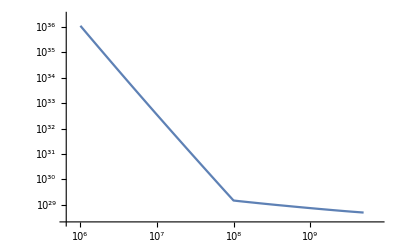

```mathematica
LogLogPlot[Convert[((Mega ElectronVolt)/vesc[WDplot[Log10[ρ]]]^2(trigger[ρ]*Centimeter)^2*ρ Gram/Centimeter^3*1/(12 Giga ElectronVolt)*SpeedOfLight^2(50Kilo Meter))1/(Giga ElectronVolt),d],{ρ,10^6,5*10^9}]
```

#### SN information

```mathematica
eboomreverse[22+Log10[10^-1]]
```

0.768666

```mathematica
snrate=0.3/Century; 
whitedwarfdistribution[m_] := 1/(0.14 Sqrt[2 π])Exp[(-(m - 0.64)^2)/(2 (0.14)^2)];
Qfunction = (FullSimplify[Re[Integrate[whitedwarfdistribution[m], {m,x, ∞}]]]);
Qcolldecay=Qfunction/.{x->(If[eboomreverse[logmdm+Log10[η]]≥ 0.85, eboomreverse[logmdm+Log10[η]], 0.85])};
```

#### Collision Constraints

```mathematica
σcollision=Γcollision ((ρdm/mdm)^2 (vesc/v)^3 v 4 Pi/3 Rwd^3)^-1;
σobsRX=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
σobsNuStar=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
```

```mathematica
σobsRX/.logmdm->eboom[1.25]
```

3.84821×10^-24

```mathematica
σobsNuStar/.logmdm->eboom[1.25]
```

6.15714×10^-31

```mathematica
σfun=Convert[σcollision*1/Century/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
σSN1=σfun/.{Γcollision->snrate*Century*1/(10^10 Qcolldecay)}/.η->1;
σSN2=σfun/.{Γcollision->snrate*Century*1/(10^10 Qcolldecay)}/.η->10^-1;
```

```mathematica
SNcollision1=Plot[Log10[σSN1],{logmdm,15.2,21},PlotStyle->{Green,Thick}];
```

```mathematica
SNcollision2=Plot[Log10[σSN2],{logmdm,16.2,21},PlotStyle->{Purple,Thick}];
```

```mathematica
RXcollision=Plot[Log10[σobsRX],{logmdm,15,21},PlotStyle->{Blue,Thick}];
NuStarcollision=Plot[Log10[σobsNuStar],{logmdm,15,21},PlotStyle->{Gray,Thick}];
```

```mathematica
eboomlimitcollision1=Plot[(100 Sign[x-(15.625-Log10[1])]),{x,15,25},ExclusionsStyle->Red,PlotRange->{-35,-10}];
```

```mathematica
eboomlimitcollision2=Plot[(100 Sign[x-(15.625-Log10[10^-1])]),{x,15,25},ExclusionsStyle->Yellow,PlotRange->{-35,-10}];
```

```mathematica
canvascollision=Plot[-100,{logmdm,15,21},Frame->True,FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_(DM - DM) (cm^2)"},PlotRange->{-35,-10},Axes->None];
```

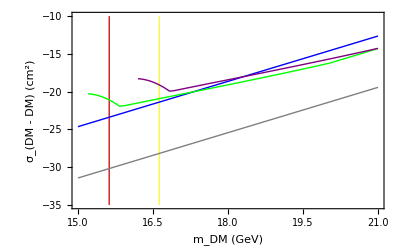

```mathematica
Show[canvascollision,eboomlimitcollision1,eboomlimitcollision2,RXcollision,NuStarcollision,SNcollision1,SNcollision2]
```

#### Decay Constraints

```mathematica
τdm=1/Γdecay(ρdm/mdm) (vesc/v)4 Pi/3 Rwd^3;
```

```mathematica
τobsRX=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
τobsNuStar=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
```

```mathematica
τobsRX/.logmdm->eboom[1.25]
```

2.5245×10^12

```mathematica
τobsNuStar/.logmdm->eboom[1.25]
```

6.31125×10^15

```mathematica
τfun=Convert[τdm*Century/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
τSN1=τfun/.{Γdecay->snrate*Century*1/(10^10 Qcolldecay)}/.η->1;
τSN2=τfun/.{Γdecay->snrate*Century*1/(10^10 Qcolldecay)}/.η->10^-1;
```

```mathematica
SNdecay1=Plot[Log10[τSN1],{logmdm,15.2,21},PlotStyle->{Green,Thick}];
```

```mathematica
SNdecay2=Plot[Log10[τSN2],{logmdm,16.2,21},PlotStyle->{Purple,Thick}];
```

```mathematica
RXdecay=Plot[Log10[τobsRX],{logmdm,15,21},PlotStyle->{Blue,Thick}];
NuStardecay=Plot[Log10[τobsNuStar],{logmdm,15,21},PlotStyle->{Gray,Thick}];
```

```mathematica
canvasdecay=Plot[-100,{logmdm,15,21},Frame->True,FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "τ_DM (Gyr)"},PlotRange->{5,18},Axes->None];
```

```mathematica
eboomlimitdecay1=Plot[(100 Sign[x-(15.625-Log10[1])]),{x,15,25},ExclusionsStyle->Red,PlotRange->{5,20}];
```

```mathematica
eboomlimitdecay2=Plot[(100 Sign[x-(15.625-Log10[10^-1])]),{x,15,25},ExclusionsStyle->Yellow,PlotRange->{5,20}];
```

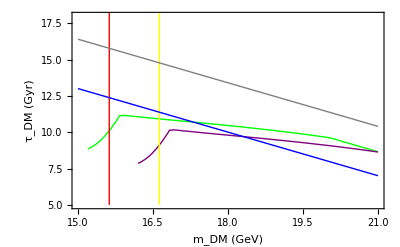

```mathematica
Show[canvasdecay,SNdecay1,SNdecay2,eboomlimitdecay1,eboomlimitdecay2,RXdecay,NuStardecay]
```

```mathematica
Transit Constraints for Subscript[L, 0]<Subscript[λ, T] - ϵ = TeV
```

```mathematica
transitreverse=Interpolation[Table[{Log10[10^-3/ϵ*triggermass[Mwd]^2],Mwd}/.{ϵ->10^3},{Mwd,0.4,1.37,0.01}],InterpolationOrder->1];
Qtransit=Qfunction/.{x->If[transitreverse[logσ]≥0.85,transitreverse[logσ], 0.85]};
transitfun=Convert[(ρdm/mdm)π Rwd^2(vesc/v)^2 v/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},1/Century];
```

```mathematica
transitreverse[-15.8]
```

1.36932

```mathematica
transitreverse[-7]
```

0.43768

```mathematica
logmdmtransit=Log10[transitfun*10^10*Qtransit 1/snrate*10^logmdm];
```

```mathematica
Table[logmdmtransit,{logσ,-11,-10.9,0.01}]
```

{46.4769,46.4832,46.4894,46.4957,46.5019,46.5081,46.5121,46.5121,46.5121,46.5121,46.5121}

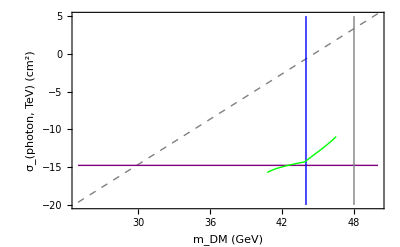

```mathematica
crust=Log10[Convert[vesc[1.25]^2/(10^32 Centimeter^-3*50Kilo Meter)10^mdm/ϵ,Centimeter^2] 1/Centimeter^2];
transitboom=Log10[10^-3/ϵ*triggermass[1.25]^2];
crustplotTeV=Plot[crust/.ϵ->10^3,{mdm,25,50},PlotStyle->{Dashed,Gray,Thick}];
photontransitTeV=Plot[transitboom/.ϵ->10^3,{mdm,25,50},PlotStyle->{Thick,Purple}];
transitSN=Interpolation[Table[{logmdmtransit,logσ},{logσ,-15.7,-10.94,0.01}]];
transitSNTeV=Plot[transitSN[logmdm],{logmdm,40.770817501701494,46.51214384627496},PlotStyle->{Green,Thick}];
fluxlimitRX=Plot[( 100 Sign[x-44]),{x,24,50},ExclusionsStyle->Blue,PlotRange->{-20,5}];
fluxlimitNuStar=Plot[( 100 Sign[x-48]),{x,24,50},ExclusionsStyle->Gray,PlotRange->{-20,5}];
canvastransit=Plot[-100,{x,25,50},Frame->True,FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_(photon, TeV) (cm^2)"},PlotRange->{-20,5},Axes->None];

Show[canvastransit,crustplotTeV,photontransitTeV,fluxlimitRX,fluxlimitNuStar,transitSNTeV]
```

#### Q-ball boom

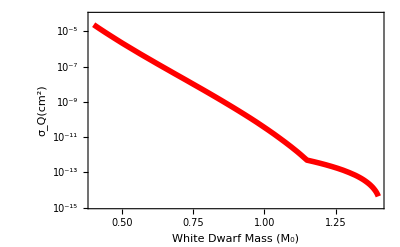

```mathematica
LogPlot[1/10^4*(triggermass[M])^2,{M,0.4,1.4},Frame->True,FrameLabel->{"White Dwarf Mass (M_0)","σ_Q(cm^2)"},FrameStyle->Black,PlotStyle-> {Red,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```